# H2, 4 qubits

## Modules

Format the hamiltonian from qiskit; daniel’s format

```mathematica
FormatHamiltonian::usage="Format the hamiltonian from qiskit;daniel's format";
FormatHamiltonian[filename_]:=Module[{stringham,ham,nterms,nqubits},
stringham=Import[filename];
ham=ToExpression[stringham];
nqubits=1+Select[Flatten[Level[#,-1]&/@Flatten@ham],NumericQ[#]&]//Max;
nterms=Length@ham;
{Total@Apply[Times,ham,1],nterms,nqubits}
]
```

## Hamiltonian generation

```mathematica
{hamiltonian,nterms,nqubits}=FormatHamiltonian["/home/cica/vqe/molecules/H2/H2.txt"];
```

```mathematica
{nqubits,nterms}
```

{4,15}

```mathematica
groundstate=Min@Eigenvalues@CalcPauliSumMatrix@hamiltonian
```

-1.13728

```mathematica
hamiltonian
```

-0.0970663-0.0453026 X_2 X_3 Y_0 Y_1+0.0453026 X_0 X_3 Y_1 Y_2+0.0453026 X_1 X_2 Y_0 Y_3-0.0453026 X_0 X_1 Y_2 Y_3+0.171413 Z_0+0.171413 Z_1+0.168689 Z_0 Z_1-0.223432 Z_2+0.120625 Z_0 Z_2+0.165928 Z_1 Z_2-0.223432 Z_3+0.165928 Z_0 Z_3+0.120625 Z_1 Z_3+0.174413 Z_2 Z_3

## The runs

```mathematica
DefaultConfig[4]
```

<|nqubit→4,methode→NG,gatespercycle→30,ngatesinit→40,fixansatz→{},fixansatzparams→<||>,ansatzspace→{0,1,2,3},weightgate→{1→0.2,2→0.8},ansatzinit→{X_0,X_1},swapfabricdepth→0,maxfevbf→100,greediness→10,greedinessinit→8,greedflat→0.01,maxgreediter→120,gradstep→0.001,dθ→0.01,gradstepmultiply→2,αtikhonov→1/10000,θignore→1/1000,metignore→1/1000,perfectingflat→0.00015,pruningerror→0.1,iterconverge→20,globalconverge→2,θinitrange→π/4,ϵfin→1/10000000,slowfirst→True,refine→2,gateset→{Rx_#1[θ]&,Ry_#1[θ]&,Rz_#1[θ]&,C_#1[Rx_#2[θ]]&,C_#1[Ry_#2[θ]]&,C_#1[Rz_#2[θ]]&}|>

```mathematica
results={};
Table[
Print["Trial ",trial];
Print@Now;
Print["target: ",groundstate];
DestroyAllQuregs[];
conf=DefaultConfig[nqubits];
{timing,{Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,elim}}=AbsoluteTiming[VQEGS[nqubits,hamiltonian,conf]];

DrawCircuit[ansatz,nqubits];
Print["runtime=",timing/3600," hours"];
Print["nansatz=",Length@ansatz];
Print["nansatz/cycle=",Length@#&/@cycleres["ansatz"]];
Print["<E>/cycle=",cycleres["E"]];
Print["ϵ/cycle=",cycleres["E"]-groundstate];
{ψ,ψwork}=CreateQuregs[nqubits,2];
ApplyCircuit[ψ,Join[conf["ansatzinit"],ansatz]/.θvars];
ecur=CalcExpecPauliSum[ψ,hamiltonian,ψwork];
Print["<E>=",ecur];
Print["<E>-E_gs=",ecur-groundstate];
DestroyAllQuregs[];
AppendTo[results,{ansatz,θvars,cycleres,fev,aborted,elim}];
ecur
,{trial,10}]
```

Trial 1

Mon 24 Jan 2022 21:11:22GMT

target: -1.13728

@cycle1, fev:556, <E>: -1.1372838344065226 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 6, 3, 23, 0}

I'm slowing down. Number of gates is increased to 36 @cycle 2

@cycle2, fev:1175, <E>: -1.1372838344065226 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 6, 3, 23, 3}

I'm slowing down. Number of gates is increased to 44 @cycle 3

@cycle3, fev:1701, <E>: -1.1372838344065226 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 6, 3, 23, 0}

runtime=0.0441569 hours

nansatz=7

nansatz/cycle={0,7,7}

<E>/cycle={-1.11676,-1.13728,-1.13728}

ϵ/cycle={0.0205245,8.19798×10^-11,8.19798×10^-11}

<E>=-1.13728

<E>-E_gs=8.19798×10^-11

Trial 2

Mon 24 Jan 2022 21:14:01GMT

target: -1.13728

@cycle1, fev:776, <E>: -1.1372838325645378 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 10, 7, 17, 1}

@cycle2, pathetic result.

I'm slowing down. Number of gates is increased to 36 @cycle 2

@cycle2, fev:989, <E>: -1.1372838325645378 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 10, 7, 17, 2}

@cycle3, pathetic result.

I'm slowing down. Number of gates is increased to 44 @cycle 3

@cycle3, fev:1415, <E>: -1.1372838325645378 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 10, 7, 17, 2}

runtime=0.0495892 hours

nansatz=6

nansatz/cycle={0,6,6}

<E>/cycle={-1.11676,-1.13728,-1.13728}

ϵ/cycle={0.0205245,1.92396×10^-9,1.92396×10^-9}

<E>=-1.13728

<E>-E_gs=1.92396×10^-9

Trial 3

Mon 24 Jan 2022 21:16:59GMT

target: -1.13728

@cycle1, fev:840, <E>: -1.137283813263961 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 9, 4, 22, 0}

@cycle2, pathetic result.

I'm slowing down. Number of gates is increased to 36 @cycle 2

@cycle2, fev:1020, <E>: -1.137283813263961 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 9, 4, 22, 0}

@cycle3, pathetic result.

I'm slowing down. Number of gates is increased to 44 @cycle 3

@cycle3, fev:1605, <E>: -1.137283813263961 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 9, 4, 22, 1}

runtime=0.0577911 hours

nansatz=5

nansatz/cycle={0,5,5}

<E>/cycle={-1.11676,-1.13728,-1.13728}

ϵ/cycle={0.0205245,2.12245×10^-8,2.12245×10^-8}

<E>=-1.13728

<E>-E_gs=2.12245×10^-8

Trial 4

Mon 24 Jan 2022 21:20:28GMT

target: -1.13728

@cycle1, fev:428, <E>: -1.1372838344748883 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 10, 14, 10, 2}

I'm slowing down. Number of gates is increased to 36 @cycle 2

@cycle2, fev:703, <E>: -1.1372838344748883 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 10, 14, 10, 1}

@cycle3, pathetic result.

I'm slowing down. Number of gates is increased to 44 @cycle 3

@cycle3, fev:1024, <E>: -1.1372838344748883 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 10, 14, 10, 0}

runtime=0.0258488 hours

nansatz=4

nansatz/cycle={0,4,4}

<E>/cycle={-1.11676,-1.13728,-1.13728}

ϵ/cycle={0.0205245,1.3614×10^-11,1.3614×10^-11}

<E>=-1.13728

<E>-E_gs=1.3614×10^-11

Trial 5

Mon 24 Jan 2022 21:22:01GMT

target: -1.13728

@cycle1, fev:564, <E>: -1.1372838314967284 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 4, 3, 29, 0}

@cycle2, pathetic result.

I'm slowing down. Number of gates is increased to 36 @cycle 2

@cycle2, fev:775, <E>: -1.1372838314967284 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 4, 3, 29, 2}

@cycle3, pathetic result.

I'm slowing down. Number of gates is increased to 44 @cycle 3

@cycle3, fev:1411, <E>: -1.1372838314967284 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 4, 3, 29, 0}

runtime=0.0527711 hours

nansatz=4

nansatz/cycle={0,4,4}

<E>/cycle={-1.11676,-1.13728,-1.13728}

ϵ/cycle={0.0205245,2.99177×10^-9,2.99177×10^-9}

<E>=-1.13728

<E>-E_gs=2.99177×10^-9

Trial 6

Mon 24 Jan 2022 21:25:11GMT

target: -1.13728

@cycle1, fev:565, <E>: -1.1372838340345877 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 12, 8, 15, 0}

@cycle2, pathetic result.

I'm slowing down. Number of gates is increased to 36 @cycle 2

@cycle2, fev:815, <E>: -1.1372838340345877 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 12, 8, 15, 0}

@cycle3, pathetic result.

I'm slowing down. Number of gates is increased to 44 @cycle 3

@cycle3, fev:1136, <E>: -1.1372838340345877 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 12, 8, 15, 3}

runtime=0.039667 hours

nansatz=5

nansatz/cycle={0,5,5}

<E>/cycle={-1.11676,-1.13728,-1.13728}

ϵ/cycle={0.0205245,4.53915×10^-10,4.53915×10^-10}

<E>=-1.13728

<E>-E_gs=4.53915×10^-10

Trial 7

Mon 24 Jan 2022 21:27:33GMT

target: -1.13728

@cycle1, fev:502, <E>: -1.137283834164124 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 6, 10, 16, 0}

@cycle2, pathetic result.

I'm slowing down. Number of gates is increased to 36 @cycle 2

@cycle2, fev:775, <E>: -1.137283834164124 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 6, 10, 16, 0}

@cycle3, pathetic result.

I'm slowing down. Number of gates is increased to 44 @cycle 3

@cycle3, fev:1064, <E>: -1.137283834164124 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 6, 10, 16, 3}

runtime=0.0373918 hours

nansatz=7

nansatz/cycle={0,7,7}

<E>/cycle={-1.11676,-1.13728,-1.13728}

ϵ/cycle={0.0205245,3.24378×10^-10,3.24378×10^-10}

<E>=-1.13728

<E>-E_gs=3.24378×10^-10

Trial 8

Mon 24 Jan 2022 21:29:48GMT

target: -1.13728

@cycle1, fev:758, <E>: -1.1372838209947456 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 3, 1, 26, 0}

@cycle2, pathetic result.

I'm slowing down. Number of gates is increased to 36 @cycle 2

@cycle2, fev:939, <E>: -1.1372838209947456 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 3, 1, 26, 0}

@cycle3, pathetic result.

I'm slowing down. Number of gates is increased to 44 @cycle 3

@cycle3, fev:1267, <E>: -1.1372838209947456 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 3, 1, 26, 0}

runtime=0.0403866 hours

nansatz=8

nansatz/cycle={0,8,8}

<E>/cycle={-1.11676,-1.13728,-1.13728}

ϵ/cycle={0.0205245,1.34938×10^-8,1.34938×10^-8}

<E>=-1.13728

<E>-E_gs=1.34938×10^-8

Trial 9

Mon 24 Jan 2022 21:32:13GMT

target: -1.13728

@cycle1, fev:767, <E>: -1.137283831041449 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 3, 6, 25, 0}

@cycle2, pathetic result.

I'm slowing down. Number of gates is increased to 36 @cycle 2

@cycle2, fev:1212, <E>: -1.137283831041449 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 3, 6, 25, 0}

@cycle3, pathetic result.

I'm slowing down. Number of gates is increased to 44 @cycle 3

@cycle3, fev:1657, <E>: -1.137283831041449 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 3, 6, 25, 0}

runtime=0.0560616 hours

nansatz=6

nansatz/cycle={0,6,6}

<E>/cycle={-1.11676,-1.13728,-1.13728}

ϵ/cycle={0.0205245,3.44705×10^-9,3.44705×10^-9}

<E>=-1.13728

<E>-E_gs=3.44705×10^-9

Trial 10

Mon 24 Jan 2022 21:35:35GMT

target: -1.13728

@cycle1, fev:816, <E>: -1.1372838279813502 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 2, 5, 23, 3}

@cycle2, pathetic result.

I'm slowing down. Number of gates is increased to 36 @cycle 2

@cycle2, fev:1003, <E>: -1.1372838279813502 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 2, 5, 23, 0}

@cycle3, pathetic result.

I'm slowing down. Number of gates is increased to 44 @cycle 3

@cycle3, fev:1402, <E>: -1.1372838279813502 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 2, 5, 23, 1}

runtime=0.0520377 hours

nansatz=8

nansatz/cycle={0,10,8}

<E>/cycle={-1.11676,-1.13728,-1.13728}

ϵ/cycle={0.0205245,6.50715×10^-9,2.45106×10^-9}

<E>=-1.13728

<E>-E_gs=2.45106×10^-9

{-1.13728,-1.13728,-1.13728,-1.13728,-1.13728,-1.13728,-1.13728,-1.13728,-1.13728,-1.13728}

## Total results

```mathematica
results
```

{{{Rx_2[θ_38],C_2[Ry_0[θ_34]],C_0[Rx_1[θ_7]],C_1[Rz_3[θ_21]],C_2[Ry_3[θ_19]],C_0[Rx_1[θ_16]],C_2[Ry_1[θ_6]]},<|θ_6→3.14159,θ_7→3.1416,θ_16→-3.14159,θ_19→-3.14159,θ_21→3.14147,θ_34→-3.14159,θ_38→0.225563|>,<|ansatz→{{},{Rx_2[θ_38],C_2[Ry_0[θ_34]],C_0[Rx_1[θ_7]],C_1[Rz_3[θ_21]],C_2[Ry_3[θ_19]],C_0[Rx_1[θ_16]],C_2[Ry_1[θ_6]]},{Rx_2[θ_38],C_2[Ry_0[θ_34]],C_0[Rx_1[θ_7]],C_1[Rz_3[θ_21]],C_2[Ry_3[θ_19]],C_0[Rx_1[θ_16]],C_2[Ry_1[θ_6]]}},θvars→{<||>,<|θ_6→3.14159,θ_7→3.1416,θ_16→-3.14159,θ_19→-3.14159,θ_21→3.14147,θ_34→-3.14159,θ_38→0.225563|>,<|θ_6→3.14159,θ_7→3.1416,θ_16→-3.14159,θ_19→-3.14159,θ_21→3.14147,θ_34→-3.14159,θ_38→0.225563|>},E→{-1.11676,-1.13728,-1.13728},idx→{1,41,41}|>,1802,{2,3},{0,6,3,23}},{{C_0[Ry_2[θ_8]],C_2[Ry_3[θ_20]],C_1[Rz_3[θ_16]],C_3[Rx_1[θ_5]],C_0[Rz_1[θ_10]],C_2[Ry_0[θ_22]]},<|θ_5→3.14184,θ_8→-0.225609,θ_10→3.13937,θ_16→1.56837,θ_20→3.14159,θ_22→3.14159|>,<|ansatz→{{},{C_0[Ry_2[θ_8]],C_2[Ry_3[θ_20]],C_1[Rz_3[θ_16]],C_3[Rx_1[θ_5]],C_0[Rz_1[θ_10]],C_2[Ry_0[θ_22]]},{C_0[Ry_2[θ_8]],C_2[Ry_3[θ_20]],C_1[Rz_3[θ_16]],C_3[Rx_1[θ_5]],C_0[Rz_1[θ_10]],C_2[Ry_0[θ_22]]}},θvars→{<||>,<|θ_5→3.14184,θ_8→-0.225609,θ_10→3.13937,θ_16→1.56837,θ_20→3.14159,θ_22→3.14159|>,<|θ_5→3.14184,θ_8→-0.225609,θ_10→3.13937,θ_16→1.56837,θ_20→3.14159,θ_22→3.14159|>},E→{-1.11676,-1.13728,-1.13728},idx→{1,41,41}|>,1543,{},{0,10,7,17}},{{C_1[Rx_2[θ_1]],Ry_0[θ_18],C_2[Ry_1[θ_7]],C_1[Ry_0[θ_21]],C_2[Rx_3[θ_28]]},<|θ_1→-0.225795,θ_7→3.14159,θ_18→-3.14159,θ_21→3.14159,θ_28→3.14159|>,<|ansatz→{{},{C_1[Rx_2[θ_1]],Ry_0[θ_18],C_2[Ry_1[θ_7]],C_1[Ry_0[θ_21]],C_2[Rx_3[θ_28]]},{C_1[Rx_2[θ_1]],Ry_0[θ_18],C_2[Ry_1[θ_7]],C_1[Ry_0[θ_21]],C_2[Rx_3[θ_28]]}},θvars→{<||>,<|θ_1→-0.225795,θ_7→3.14159,θ_18→-3.14159,θ_21→3.14159,θ_28→3.14159|>,<|θ_1→-0.225795,θ_7→3.14159,θ_18→-3.14159,θ_21→3.14159,θ_28→3.14159|>},E→{-1.11676,-1.13728,-1.13728},idx→{1,41,41}|>,1718,{},{0,9,4,22}},{{C_0[Rx_3[θ_26]],C_3[Ry_2[θ_7]],C_3[Ry_1[θ_11]],C_2[Rx_0[θ_5]]},<|θ_5→3.14159,θ_7→-3.14159,θ_11→-3.14159,θ_26→-0.225571|>,<|ansatz→{{},{C_0[Rx_3[θ_26]],C_3[Ry_2[θ_7]],C_3[Ry_1[θ_11]],C_2[Rx_0[θ_5]]},{C_0[Rx_3[θ_26]],C_3[Ry_2[θ_7]],C_3[Ry_1[θ_11]],C_2[Rx_0[θ_5]]}},θvars→{<||>,<|θ_5→3.14159,θ_7→-3.14159,θ_11→-3.14159,θ_26→-0.225571|>,<|θ_5→3.14159,θ_7→-3.14159,θ_11→-3.14159,θ_26→-0.225571|>},E→{-1.11676,-1.13728,-1.13728},idx→{1,41,41}|>,1106,{2},{0,10,14,10}},{{C_1[Ry_3[θ_12]],C_3[Rx_2[θ_23]],C_2[Ry_0[θ_15]],C_2[Rx_1[θ_36]]},<|θ_12→-0.225652,θ_15→3.14159,θ_23→-3.14159,θ_36→-3.14159|>,<|ansatz→{{},{C_1[Ry_3[θ_12]],C_3[Rx_2[θ_23]],C_2[Ry_0[θ_15]],C_2[Rx_1[θ_36]]},{C_1[Ry_3[θ_12]],C_3[Rx_2[θ_23]],C_2[Ry_0[θ_15]],C_2[Rx_1[θ_36]]}},θvars→{<||>,<|θ_12→-0.225652,θ_15→3.14159,θ_23→-3.14159,θ_36→-3.14159|>,<|θ_12→-0.225652,θ_15→3.14159,θ_23→-3.14159,θ_36→-3.14159|>},E→{-1.11676,-1.13728,-1.13728},idx→{1,41,41}|>,1493,{},{0,4,3,29}},{{Rx_3[θ_10],C_3[Rx_2[θ_21]],C_2[Ry_1[θ_24]],C_3[Rx_0[θ_25]],C_2[Rz_3[θ_35]]},<|θ_10→-0.225584,θ_21→-3.14159,θ_24→-3.14159,θ_25→-3.14159,θ_35→9.42503|>,<|ansatz→{{},{Rx_3[θ_10],C_3[Rx_2[θ_21]],C_2[Ry_1[θ_24]],C_3[Rx_0[θ_25]],C_2[Rz_3[θ_35]]},{Rx_3[θ_10],C_3[Rx_2[θ_21]],C_2[Ry_1[θ_24]],C_3[Rx_0[θ_25]],C_2[Rz_3[θ_35]]}},θvars→{<||>,<|θ_10→-0.225584,θ_21→-3.14159,θ_24→-3.14159,θ_25→-3.14159,θ_35→9.42503|>,<|θ_10→-0.225584,θ_21→-3.14159,θ_24→-3.14159,θ_25→-3.14159,θ_35→9.42503|>},E→{-1.11676,-1.13728,-1.13728},idx→{1,41,41}|>,1234,{},{0,12,8,15}},{{C_0[Rx_3[θ_11]],C_1[Ry_2[θ_15]],C_2[Rz_3[θ_36]],Rx_3[θ_31],C_2[Rx_0[θ_14]],C_3[Ry_1[θ_18]],C_3[Rz_0[θ_10]]},<|θ_10→3.14151,θ_11→1.5708,θ_14→-3.14159,θ_15→-0.225539,θ_18→-3.14159,θ_31→-1.5708,θ_36→3.14159|>,<|ansatz→{{},{C_0[Rx_3[θ_11]],C_1[Ry_2[θ_15]],C_2[Rz_3[θ_36]],Rx_3[θ_31],C_2[Rx_0[θ_14]],C_3[Ry_1[θ_18]],C_3[Rz_0[θ_10]]},{C_0[Rx_3[θ_11]],C_1[Ry_2[θ_15]],C_2[Rz_3[θ_36]],Rx_3[θ_31],C_2[Rx_0[θ_14]],C_3[Ry_1[θ_18]],C_3[Rz_0[θ_10]]}},θvars→{<||>,<|θ_10→3.14151,θ_11→1.5708,θ_14→-3.14159,θ_15→-0.225539,θ_18→-3.14159,θ_31→-1.5708,θ_36→3.14159|>,<|θ_10→3.14151,θ_11→1.5708,θ_14→-3.14159,θ_15→-0.225539,θ_18→-3.14159,θ_31→-1.5708,θ_36→3.14159|>},E→{-1.11676,-1.13728,-1.13728},idx→{1,41,41}|>,1177,{},{0,6,10,16}},{{C_0[Rx_2[θ_40]],Ry_3[θ_33],C_2[Ry_0[θ_22]],C_2[Ry_1[θ_12]],C_0[Ry_3[θ_34]],C_1[Rz_3[θ_6]],C_0[Rz_3[θ_4]],C_0[Rz_1[θ_39]]},<|θ_4→-2.32948,θ_6→1.42289,θ_12→-3.14159,θ_22→3.14158,θ_33→3.14152,θ_34→3.14181,θ_39→2.23504,θ_40→0.225412|>,<|ansatz→{{},{C_0[Rx_2[θ_40]],Ry_3[θ_33],C_2[Ry_0[θ_22]],C_2[Ry_1[θ_12]],C_0[Ry_3[θ_34]],C_1[Rz_3[θ_6]],C_0[Rz_3[θ_4]],C_0[Rz_1[θ_39]]},{C_0[Rx_2[θ_40]],Ry_3[θ_33],C_2[Ry_0[θ_22]],C_2[Ry_1[θ_12]],C_0[Ry_3[θ_34]],C_1[Rz_3[θ_6]],C_0[Rz_3[θ_4]],C_0[Rz_1[θ_39]]}},θvars→{<||>,<|θ_4→-2.32948,θ_6→1.42289,θ_12→-3.14159,θ_22→3.14158,θ_33→3.14152,θ_34→3.14181,θ_39→2.23504,θ_40→0.225412|>,<|θ_4→-2.32948,θ_6→1.42289,θ_12→-3.14159,θ_22→3.14158,θ_33→3.14152,θ_34→3.14181,θ_39→2.23504,θ_40→0.225412|>},E→{-1.11676,-1.13728,-1.13728},idx→{1,41,41}|>,1490,{},{0,3,1,26}},{{C_0[Ry_3[θ_18]],C_3[Ry_2[θ_23]],C_3[Rx_0[θ_26]],C_1[Rz_0[θ_37]],C_3[Ry_1[θ_38]],C_1[Rz_3[θ_40]]},<|θ_18→-0.225658,θ_23→3.14159,θ_26→-3.14159,θ_37→0.242613,θ_38→3.14159,θ_40→3.62682|>,<|ansatz→{{},{C_0[Ry_3[θ_18]],C_3[Ry_2[θ_23]],C_3[Rx_0[θ_26]],C_1[Rz_0[θ_37]],C_3[Ry_1[θ_38]],C_1[Rz_3[θ_40]]},{C_0[Ry_3[θ_18]],C_3[Ry_2[θ_23]],C_3[Rx_0[θ_26]],C_1[Rz_0[θ_37]],C_3[Ry_1[θ_38]],C_1[Rz_3[θ_40]]}},θvars→{<||>,<|θ_18→-0.225658,θ_23→3.14159,θ_26→-3.14159,θ_37→0.242613,θ_38→3.14159,θ_40→3.62682|>,<|θ_18→-0.225658,θ_23→3.14159,θ_26→-3.14159,θ_37→0.242613,θ_38→3.14159,θ_40→3.62682|>},E→{-1.11676,-1.13728,-1.13728},idx→{1,41,41}|>,1800,{},{0,3,6,25}},{{Rx_3[θ_14],C_1[Rx_2[θ_10]],Rx_1[θ_24],C_2[Rz_3[θ_20]],C_0[Ry_2[θ_22]],Rx_2[θ_23],C_3[Rx_0[θ_36]],C_0[Ry_1[θ_37]]},<|θ_10→1.57094,θ_14→-0.225635,θ_20→3.14161,θ_22→4.71254,θ_23→3.14156,θ_24→-3.14159,θ_36→-3.14159,θ_37→-3.14159|>,<|ansatz→{{},{Rx_3[θ_14],C_1[Rx_2[θ_10]],C_3[Rz_0[θ_19]],Rx_1[θ_24],C_2[Rz_3[θ_20]],C_0[Ry_2[θ_22]],Rx_2[θ_23],C_3[Rx_0[θ_36]],C_0[Ry_1[θ_37]],C_3[Rz_1[θ_39]]},{Rx_3[θ_14],C_1[Rx_2[θ_10]],Rx_1[θ_24],C_2[Rz_3[θ_20]],C_0[Ry_2[θ_22]],Rx_2[θ_23],C_3[Rx_0[θ_36]],C_0[Ry_1[θ_37]]}},θvars→{<||>,<|θ_10→1.5708,θ_14→0.225439,θ_19→-5.49422,θ_20→3.14158,θ_22→4.71239,θ_23→3.1416,θ_24→-3.14159,θ_36→-3.14159,θ_37→-3.14159,θ_39→0.788954|>,<|θ_10→1.57094,θ_14→-0.225635,θ_20→3.14161,θ_22→4.71254,θ_23→3.14156,θ_24→-3.14159,θ_36→-3.14159,θ_37→-3.14159|>},E→{-1.11676,-1.13728,-1.13728},idx→{1,41,41}|>,1709,{},{0,2,5,25}}}

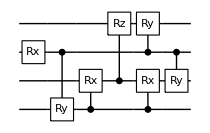
-Graphics-<|θ_6→3.14159,θ_7→3.1416,θ_16→-3.14159,θ_19→-3.14159,θ_21→3.14147,θ_34→-3.14159,θ_38→0.225563|>

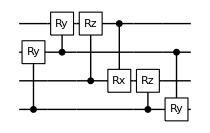
-Graphics-<|θ_5→3.14184,θ_8→-0.225609,θ_10→3.13937,θ_16→1.56837,θ_20→3.14159,θ_22→3.14159|>

-Graphics-<|θ_1→-0.225795,θ_7→3.14159,θ_18→-3.14159,θ_21→3.14159,θ_28→3.14159|>

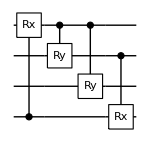
-Graphics-<|θ_5→3.14159,θ_7→-3.14159,θ_11→-3.14159,θ_26→-0.225571|>

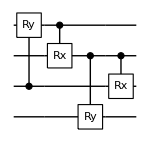
-Graphics-<|θ_12→-0.225652,θ_15→3.14159,θ_23→-3.14159,θ_36→-3.14159|>

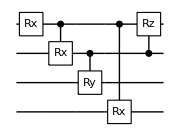
-Graphics-<|θ_10→-0.225584,θ_21→-3.14159,θ_24→-3.14159,θ_25→-3.14159,θ_35→9.42503|>

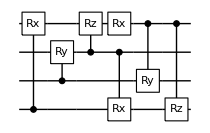
-Graphics-<|θ_10→3.14151,θ_11→1.5708,θ_14→-3.14159,θ_15→-0.225539,θ_18→-3.14159,θ_31→-1.5708,θ_36→3.14159|>

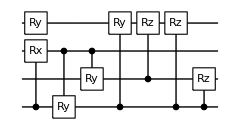
-Graphics-<|θ_4→-2.32948,θ_6→1.42289,θ_12→-3.14159,θ_22→3.14158,θ_33→3.14152,θ_34→3.14181,θ_39→2.23504,θ_40→0.225412|>

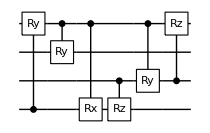
-Graphics-<|θ_18→-0.225658,θ_23→3.14159,θ_26→-3.14159,θ_37→0.242613,θ_38→3.14159,θ_40→3.62682|>

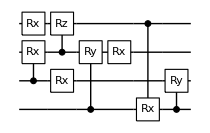
-Graphics-<|θ_10→1.57094,θ_14→-0.225635,θ_20→3.14161,θ_22→4.71254,θ_23→3.14156,θ_24→-3.14159,θ_36→-3.14159,θ_37→-3.14159|>

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Table[
Print[DrawCircuit[r[[1]],4],r[[2]]]
,{r,results}]
```

```mathematica
{ψ,ψwork}=CreateQuregs[4,2];
ansatzinit={Subscript[X, 0],Subscript[X, 1]};
chemacc=1.6*10^-3;
trial=1;
disp1=Table[
ApplyCircuit[InitZeroState@ψ,Join[ansatzinit,res⟦1⟧]/.res⟦2⟧];
ϵgs=CalcExpecPauliSum[ψ,hamiltonian,ψwork]-groundstate;
{trial++,
ϵgs<chemacc,
ϵgs,
Length@res⟦1⟧,
ToString[res⟦-1⟧],
ToString[res⟦-3⟧],
ToString[Length[#]&/@res⟦3⟧⟦"ansatz"⟧],
ToString[res⟦-2⟧]
}
,{res,results}];
PrependTo[disp1,{"trial","chemacc?","ϵgs","ngates", "elims","fevs","ngates/pcycle","aborted cycle"}];
DestroyAllQuregs[]
```

```mathematica
disp1//TableForm
```

trial | chemacc? | ϵgs | ngates | elims | fevs | ngates/pcycle | aborted cycle
1 | True | 8.19798×10^-11 | 7 | {0, 6, 3, 23} | 1802 | {0, 7, 7} | {2, 3}
2 | True | 1.92396×10^-9 | 6 | {0, 10, 7, 17} | 1543 | {0, 6, 6} | {}
3 | True | 2.12245×10^-8 | 5 | {0, 9, 4, 22} | 1718 | {0, 5, 5} | {}
4 | True | 1.3614×10^-11 | 4 | {0, 10, 14, 10} | 1106 | {0, 4, 4} | {2}
5 | True | 2.99177×10^-9 | 4 | {0, 4, 3, 29} | 1493 | {0, 4, 4} | {}
6 | True | 4.53915×10^-10 | 5 | {0, 12, 8, 15} | 1234 | {0, 5, 5} | {}
7 | True | 3.24378×10^-10 | 7 | {0, 6, 10, 16} | 1177 | {0, 7, 7} | {}
8 | True | 1.34938×10^-8 | 8 | {0, 3, 1, 26} | 1490 | {0, 8, 8} | {}
9 | True | 3.44705×10^-9 | 6 | {0, 3, 6, 25} | 1800 | {0, 6, 6} | {}
10 | True | 2.45106×10^-9 | 8 | {0, 2, 5, 25} | 1709 | {0, 10, 8} | {}